# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\bloch sphere

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# XXZ Chain

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=2;
caometer=Table[haar[1],{i,ale}];
ψTc=RandomChainProductState[L-1];
```

```mathematica
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
```

```mathematica
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
tf=10.0;
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψc},{t,0,tf,0.1}];
```

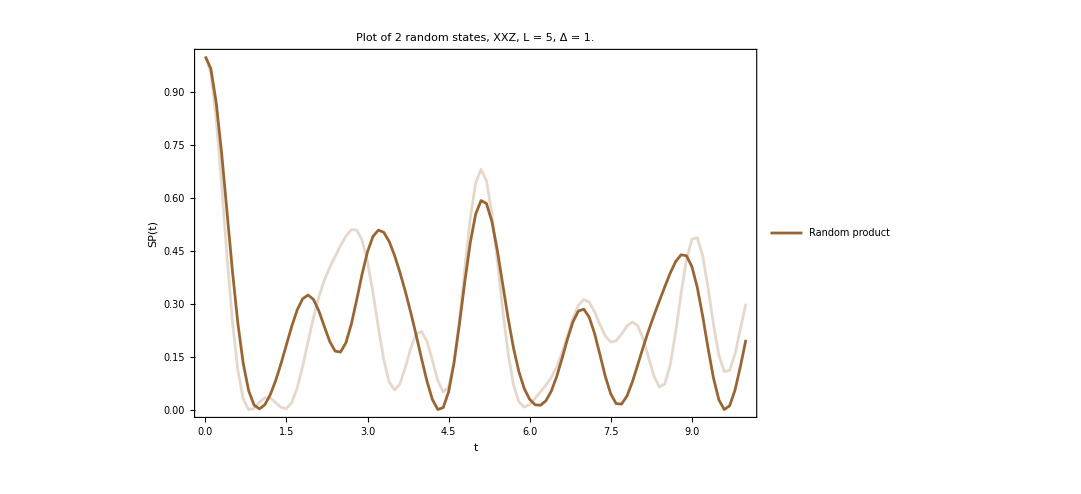

```mathematica
singlec=ListPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown],Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
traceDistance[rho_,sigma_]:=1/2*Tr[MatrixPower[ConjugateTranspose[rho-sigma].(rho-sigma),1/2]];
```

```mathematica
tracedis=Table[traceDistance[i,Dyad[caometer[[1]]]],{i,reducedc}];
```

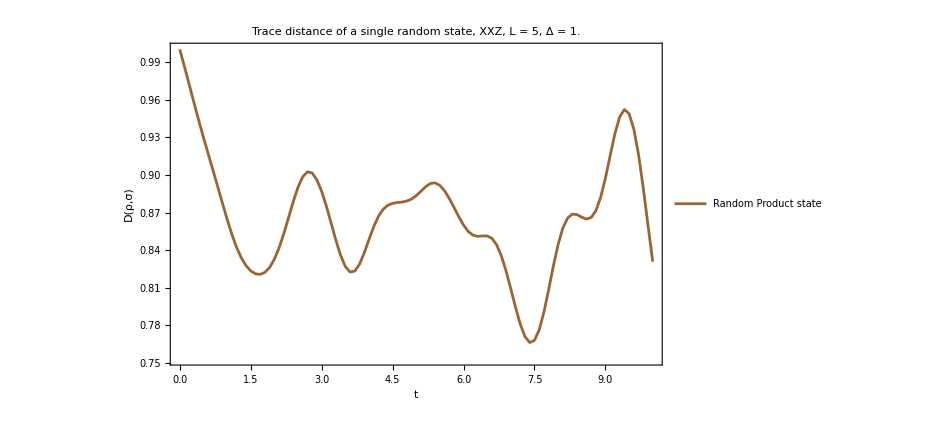

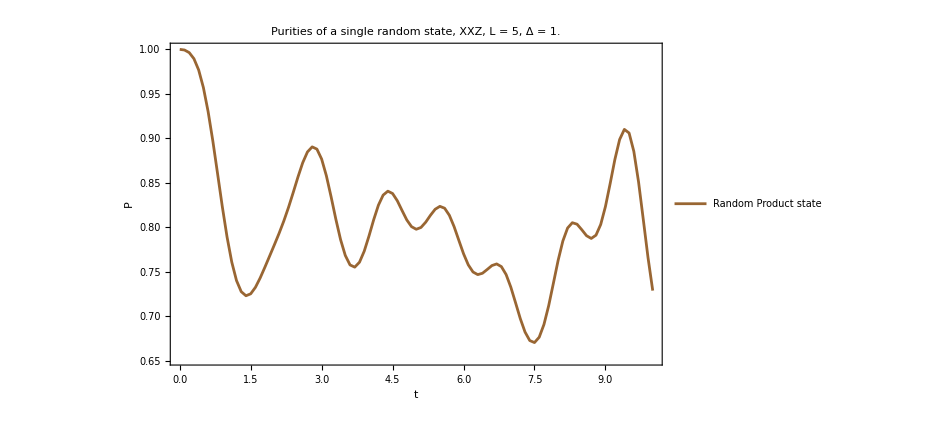

```mathematica
ListPlot[Transpose[{tlist,1-tracedis}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Trace distance of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["D(ρ,σ)"]}]

ListPlot[Transpose[{tlist,puritiesc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

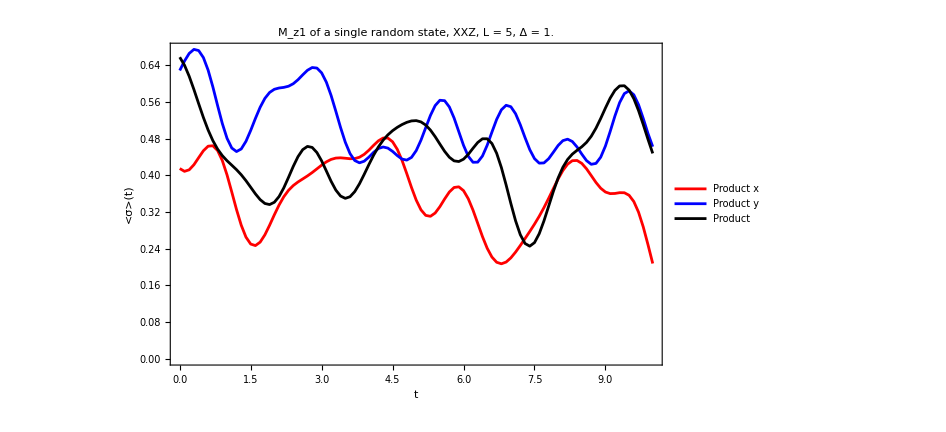

```mathematica
ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]
```

# Quantum channel xxz

## Sweep XXZ various chaometer states (only random product state)

```mathematica
L=5;
ψe=RandomChainProductState[L-1];
```

```mathematica
tf=50.;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ale=100;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
(*QUANTUM CHANNEL*)
styles={Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};
(*For each initial state compute bloch sphere dynamics and export it as video*)
   figs={};
listplots={};
purities={};
directionsx={};
directionsy={};
directionsz={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
choidirectionsx={};
choidirectionsy={};
choidirectionsz={};

Do[
superOp=Superoperator[t,ψe,eigenval,eigenvec,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,.1}];

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];

AppendTo[purities,Show[{
ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];
,{i,1}];
```

```mathematica
allpurities={};
Do[

(*REDUCED DYNAMICS*)
ψc=Flatten[KroneckerProduct[caometer[[i]],ψe]];
ψct=Table[StateEvolution[t,ψc,eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
AppendTo[allpurities,puritiesc];
,{i,Length[caometer]}];
```

```mathematica
tlist=Range[0,tf,0.1];
puritiesplot=ListPlot[Table[Transpose[{tlist,Chop[i]}],{i,allpurities}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[0.05]],PlotRange->All,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
puritymeanplot=ListPlot[Transpose[{tlist,Mean[allpurities]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[1]],PlotRange->All,PlotLegends->{Style["Random Product state",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
purityplot=Show[{puritymeanplot,puritiesplot},PlotRange->{All,{0.48,1.01}}];
```

```mathematica
testimage=Grid[{{listplots,purities,purityplot}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

## Stationary point

```mathematica
data1={};
data2={};
data3={};
Do[
superOp=Superoperator[t,ψe,eigenval,eigenvec,L];
AppendTo[choiEigenvalues,Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[data1,Transpose[Sort[Transpose[Eigensystem[superOp]]]]];
,{t,0,tf,.1}];
```

```mathematica
eigenvalues=Table[data1[[i,1]],{i,Length[data1]}];
eigenvectors=Table[data1[[i,2]],{i,Length[data1]}];
```

```mathematica
plots=Table[ComplexListPlot[eigenvalues[[1;;i]],PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Gray],{i,Length[data1]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

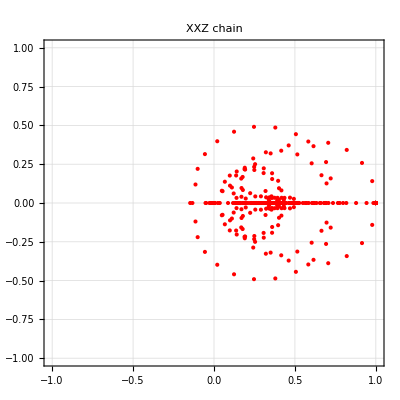

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Red,PlotLabel->Style["XXZ chain",25,Black]]
```

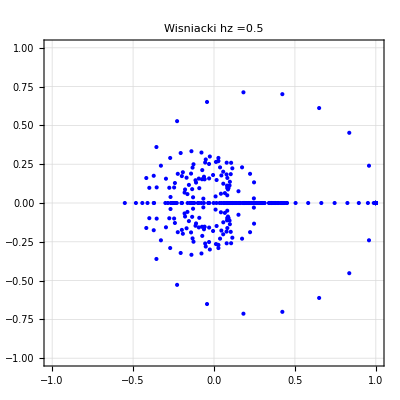

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz],25,Black]]
```

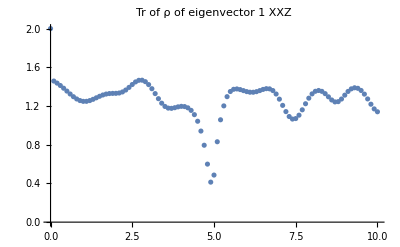

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,10,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1 XXZ", Black,18],PlotRange->All]
```

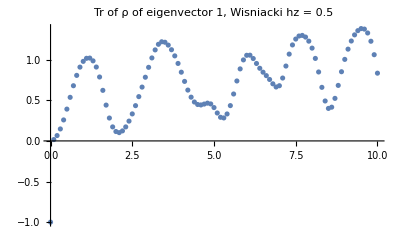

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,10,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1, Wisniacki hz = "<>ToString[hz], Black,18],PlotRange->All]
```